# Simulating a Classical Bit Flip Code

### Noisy classical channels

Consider a message, represented as an array of zeros and ones, that we want to transmit through a noisy communication channel.

The noisy channel defined by

```mathematica
ClearAll["Global`*"]
noisychannel[i_]:=Module[{p=0.1},Which[i==1,RandomChoice[{p,1-p}->{0,1}],i==0,RandomChoice[{p,1-p}->{1,0}]]]
```

This code takes input values 0,1 and outputs the array with a p=9/10 success rate. There is a 10% chance of a bit flip error so that a 0 gets flipped into a 1 and vice-versa. To see how this noisy channel in action, lets take a large, arbitrary, array of zeros and ones for our message and feed it into the noisy channel (for illustration, we print out the first 20 entries  in each array)

```mathematica
zerosandones=Table[RandomInteger[],{i,1,1000}];
Table[zerosandones[[i]],{i,1,20}]
```

{0,0,1,1,1,0,0,1,0,1,0,1,1,1,1,1,1,1,1,0}

```mathematica
transmitted=Table[noisychannel[zerosandones[[i]]],{i,1,1000}];
Table[transmitted[[i]],{i,1,20}]
```

{0,0,1,1,0,0,0,1,0,1,0,1,1,1,1,1,1,1,1,0}

We compare the original with the transmitted values by taking their difference

```mathematica
diff=Abs[transmitted-zerosandones];
Table[diff[[i]],{i,1,20}]
```

{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Obviously, the ones represent the occurrence of a bit flip error. We can be more quantitative by counting the number of errors

{{0,907},{1,93}}

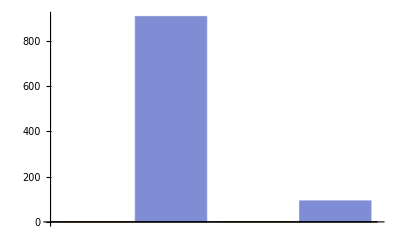

```mathematica
stats=Tally[diff]
BarChart[stats]
```

The Bar chart illustrates the relative outcomes for the corrupted  and unblemished bits. According to the frequency interpretation, we assign the probabilities   p=#errors/total  1-p = #successes/total

```mathematica
probabilityoferror=N[stats[[2,2]]/(stats[[1,2]]+stats[[2,2]])]
```

0.093

### Encoding

Let’s take a simple message

```mathematica
message={1,0,1,0,0,1,1,1,0,0};
n=Dimensions[message][[1]];
```

We now encode our message using the 3-bit code words 0→000 and 1→111.

```mathematica
code=Flatten[Table[{message[[i]],message[[i]],message[[i]]},{i,1,n}]]
```

{1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0}

### Transmission

The code is now transmitted through the noisy channel. Here register output2 is the transmitted message expressed in terms of its codewords

```mathematica
output1=Table[noisychannel[code[[i]]],{i,1,3n}]
output2=Partition[output1,3]
```

{1,1,1,0,0,0,1,1,1,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0}

{{1,1,1},{0,0,0},{1,1,1},{0,1,0},{0,0,0},{1,1,1},{1,1,1},{1,1,1},{0,0,0},{0,0,0}}

### Syndrome

We prepare our code for a syndrome measurement. To that end we assign relative parities, as illustrated In Table 9.2

```mathematica
parity=Partition[-output1 /. {0->1},3]
```

{{-1,-1,-1},{1,1,1},{-1,-1,-1},{1,-1,1},{1,1,1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{1,1,1},{1,1,1}}

We define the following functions

```mathematica
p12[i_]:=parity[[i]][[3]] parity[[i]][[2]]
p13[i_]:=parity[[i]][[1]] parity[[i]][[3]]
flip[i_]:=If[i==0,1,0]
paritytable:=Table[{p12[i],p13[i]},{i,1,n}];
```

To facilitate our syndrome analysis, for which we define the function syndrome[] below, we adhere to the algorithm described in Fig. 9.2 above.

```mathematica
syndrome[i_]:=Which[paritytable[[i]][[1]]==1 && paritytable[[i]][[2]] ==1,output2[[i]],paritytable[[i]][[1]]==-1 && paritytable[[i]][[2]] ==-1,ReplacePart[output2[[i]],3->flip[output2[[i]][[3]]]],paritytable[[i]][[1]]==-1 && paritytable[[i]][[2]] ==1,ReplacePart[output2[[i]],2->flip[output2[[i]][[2]]]],paritytable[[i]][[1]]==1 && paritytable[[i]][[2]] ==-1,ReplacePart[output2[[i]],1->flip[output2[[i]][[1]]]]]
```

The command   syndrome[i] performs a syndrome measurement of the i’th codeword (starting with i=1 at the left most side of the code), e.g. for code output2

### Error correction

Having constructed our syndrome function, we feed each codeword of the code output2 into our syndrome

```mathematica
output3=Table[syndrome[i],{i,1,n}]
```

{{1,1,1},{0,0,0},{1,1,1},{0,0,0},{0,0,0},{1,1,1},{1,1,1},{1,1,1},{0,0,0},{0,0,0}}

which we can map back into a message with the substitution 000 → 0, 111 →1

```mathematica
cmessage=output3 /. {{0,0,0}->0,{1,1,1}->1}
```

{1,0,1,0,0,1,1,1,0,0}

Comparing the corrected message,cmessage, with the original

```mathematica
message
cmessage
```

{1,0,1,0,0,1,1,1,0,0}

{1,0,1,0,0,1,1,1,0,0}

```mathematica
{1,0,1,0,0,1,1,1,0,0}
```

{1,0,1,0,0,1,1,1,0,0}

We find that the 3 bit code corrects single bit flip errors.  The above message is too short for good statistics, so lets transmit a message containing 1000 bits.  Encoding the bits into a 3-bit code, the transmitted message is subjected to the error syndrome described above. The following

First construct a random message

```mathematica
message=Table[RandomInteger[],{i,1,1000}];
n=Dimensions[message][[1]];
code=Flatten[Table[{message[[i]],message[[i]],message[[i]]},{i,1,n}]];
```

Encode, take syndrome measurements, and correct

```mathematica
output1=Table[noisychannel[code[[i]]],{i,1,3n}];
output2=Partition[output1,3];
parity=Partition[-output1 /. {0->1},3];
output3=Table[syndrome[i],{i,1,n}];
cmessage=output3 /. {{0,0,0}->0,{1,1,1}->1};
```

Compare corrected message with original

```mathematica
stats=Tally[Abs[cmessage-message]]
probabilityoferror=N[stats[[2,2]]/(stats[[1,2]]+stats[[2,2]])]
```

{{0,973},{1,27}}

0.027

Thus we notice that the probability for a bit flip error is on the order of 3 %, in harmony with the prediction that the 3 bit code reduces the error p (10 %) to the value 3p^2(1-p), or about 3 %.

Exercise 1.  Demonstrate this scaling for various values of p